```mathematica
data =Import["/home/ilya/brusselator/brus.dat", "Table"];
srezdata = Cases[data,{_ (*t_ /; (t>=0.03)&&(t<0.04)*),x_ /; x==a  ,_,_}/.a-> 0.40];
tdata = srezdata⟦All, 1⟧;
udata = srezdata⟦All, 3⟧;
listTU =Transpose[{tdata,udata}];
ListLinePlot[listTU]
ListContourPlot[data⟦All,1;;3⟧]
```

-Graphics-

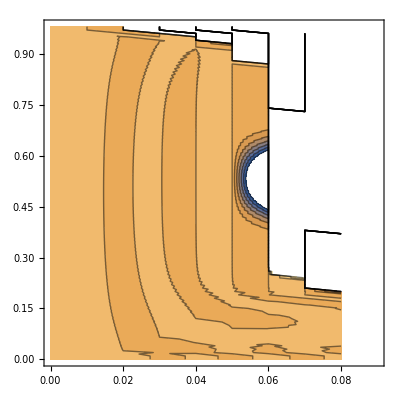

```mathematica
Export["/home/ilya/brusselator/plots/b=3nonlinsimplex040.png",ListLinePlot[listTU]];
Export["/home/ilya/brusselator/plots/b=3nonlinsimplex0043d.png",ListContourPlot[data⟦All,1;;3⟧]];
```

```mathematica
tdata = data⟦All, 1⟧;
xdata = data⟦All, 2⟧;
udata = data⟦All, 3⟧;
vdata = data⟦All, 4⟧;
```

```mathematica
Length@tdata
```

10000

```mathematica
data⟦1;;5⟧
```

{{0.,0.,1.,3.},{0.,0.01,1.,3.},{0.,0.02,1.,3.},{0.,0.03,1.,3.},{0.,0.04,1.,3.}}

```mathematica
udata⟦102⟧
```

0.231107

```mathematica
srezdata = Cases[data,{_ (*t_ /; (t>=0.03)&&(t<0.04)*),x_ /; (x≥0.40)&&(x<0.41)  ,_,_}]
```

{{0.,0.4,1.,1.},{0.01,0.4,0.986608,-1946.68},{0.02,0.4,0.019399,3862.43},{0.03,0.4,0.000565,-7655.02},{0.04,0.4,-0.000266,15157.5},{0.05,0.4,2.4377454309360445813×10^14,-29984.},{0.06,0.4,-3.88216861939937532512322495916487545166018746145625915649035337728×10^65,1.18913×10^10},{0.07,0.4,1.567951907754957209813927597599035320110708402529347301884758769906054372931568553827608800686142367081666686352018620643780967071501083414898891087796120734426683537121001236674548705578196990685702750139968608163332096×10^219,-1.8937158522439354256473306279947741050650829550116513645592576×10^61},{0.08,0.4,-1.03301771523590004962428880222093058240104659630795618407429101187618016716132648458421023188505923652521196372359690378417132727683385644119228585328246897445176116622753795415978844034699155295876331090306343617000125120378008419752550981848136836393548475327309729008503182297540060202572388567985287623392816270989870124876615620738627781846321262652824719792294473119127937862320077496512448353971879637272469680720698617687026926744982848631360305111299502339007008119012338645070566874436862812805478017635228946650647532041811838637583396762862463206426425778207209701376138072349153456367720493403276874595336899580990637254588541706105758463645868019662913876395753996288×10^680,7.6484451781404984475745073017901872033822858236467239032344086983357529127090610246881523917789958191498201320111253773172376453264940438632411520150277010544206905314525044555661820143237554734408619900283327086592×10^214},{0.09,0.4,2.9541521791700694315795955025540934898454432828491539430826853493475877691355946370297079424339945221592993361802659186934110784219381404732807820090610952371190936810888333842238186146262357416231396375761102156512595633971201421364317260833114726624006258728366725311838035325841253254466137110549413740549936195774042623200436625397480865978233466983032322652277918053432641241504228167405418785503571838206668733208876308589928962487541726399300756429767145075120574620037150994617986096715989791582466129890205188748002785563340847278506106868144034786478222719267725593917948127880648071789894561500494609486244079866622664683459934099655569215261361801964082785382054124976526742564503524441016406007578282218544140960632242424035104393263703253949816736707190163993309043768709125663955421035566740967018707955806215933634455564840314099832524493446537354047857459122685353498878205015802676568300884376786400185346427785068418163044841639765468600428310310068345796973707323937767817420808846263789902737939729284435334831417228663007848681851763093774575604313109553148676454535525104292551271367668907643196537593002726419509718532544583040868721560126465537893479733230321188380047134734412110860566150664259609987184590601632549617917167461088655037800043926280804683542766244925006869232342974633201779176897947974628384007389058997425586137649749210509697246989031238275951870155708945301652590559346092785662943007878527989814338860061465412353712536729476619728717208634494486906192094258129060133413541443037943882964199477319522118611496513394161563132551435611073584887598104494806851348626539296685451355326940377462355734277212231874399383336613357148209211990632764319093658037604986386626809599454744766416942747692725769051903921344723423597701973709597991556246600698673338006161582113537794773682643551036799098895311586584249153180266985081181820341100695696956378367876665185788575780410353637697242076449168982368927413353275125655057103855522805559741688209072994252068173754865014005794516813128016931772258657649274053881646546944×10^2062,-5.039044452842063621682082924549908416843610524738418389363480933831887812207694815915295962352872354988293772470384118679059089732428495943343338384669900203043635093885264114780496124707566377702075617527382012048750197896368368661692437256144826320709355519464410696098202534477348670663921460488408330054641516971938353559493881832506065739149608813072812500617909766050007484288075955417490013352801565364823341623674875751766588944542307851025879487871548506038280956400882012754164523332305524626376886380489459840589984479731925782210121469496436072621725066029890142277143561965285392087672274939145638471842620835821275074083272426852574279835417853397382722830204928×10^675},{0.1,0.4,-inf,1.441030868275097423669793330333529969907060620990720531990739172010827887563767283810819500869452266105127046566314614370244880478388739279385992585655029567463744721150661216705885785962493519316498489681470664198448604215128154002057264170697072372515472033786427073144578393497543164398451493510771336762959644825169802360225888766686208792081552619400905756446569208248484560651919545627328372286432907011163714482122531164154448091345414762250382800158127907629208162704733837611384886261051529701985836008614620449991717296414920214384362238433889325068356515923141764540868433162940181482062425500660761060847182003890330378158544308884496392419313010030229892332615869814685057824004783373665536936274661454266480478153555927901762103853739051982525819526981527666685630794931489447122585414131975396118872282237593732583227084309283911085883149168830579191782594134933858789539250874649220250950530584575223187664228059661476316042383313830251494676532564781052443689994092146686181457937220319805558339572266608085738103229201551199595085543694030997717150579232654908991003366930588476208890640707549192110543267300679075059018306147291138851812663749261290123654788374127165994498678124100360515169986881496611634391276456546797591082417174366142940593412378194057823458329520823473276937315530313307798207322408649241815872614052031890192032559696418692853385511150518010808460464190521250708878159134334372623230167325532207288003513576492529207503629110801878969900796377265094477501140220816793095090424817821703836683712406703886990920976930899991635535716552086571249652534710871625093377213175150113341684880398338258642717884421097303535468796568490833095843416656562739314527945651495208999907308869603972458232308489442182467164529984367763738942966358705454081788059211693541462355846812152659737735355045435961652277561800158791909384061262833076970787311695956985788183398274631038227892243203149465228031788925571153558706774327727883711448039774426978526225595721796183022546492871168506513949484239950130829971360528839845087281152×10^2058},{0.11,0.4,-nan,-inf},{0.12,0.4,-nan,-nan},{0.13,0.4,nan,-nan},{0.14,0.4,nan,nan},{0.15,0.4,nan,nan},{0.16,0.4,nan,nan},{0.17,0.4,nan,nan},{0.18,0.4,nan,nan},{0.19,0.4,nan,nan},{0.2,0.4,nan,nan},{0.21,0.4,nan,nan},{0.22,0.4,nan,nan},{0.23,0.4,nan,nan},{0.24,0.4,nan,nan},{0.25,0.4,nan,nan},{0.26,0.4,nan,nan},{0.27,0.4,nan,nan},{0.28,0.4,nan,nan},{0.29,0.4,nan,nan},{0.3,0.4,nan,nan},{0.31,0.4,nan,nan},{0.32,0.4,nan,nan},{0.33,0.4,nan,nan},{0.34,0.4,nan,nan},{0.35,0.4,nan,nan},{0.36,0.4,nan,nan},{0.37,0.4,nan,nan},{0.38,0.4,nan,nan},{0.39,0.4,nan,nan},{0.4,0.4,nan,nan},{0.41,0.4,nan,nan},{0.42,0.4,nan,nan},{0.43,0.4,nan,nan},{0.44,0.4,nan,nan},{0.45,0.4,nan,nan},{0.46,0.4,nan,nan},{0.47,0.4,nan,nan},{0.48,0.4,nan,nan},{0.49,0.4,nan,nan},{0.5,0.4,nan,nan},{0.51,0.4,nan,nan},{0.52,0.4,nan,nan},{0.53,0.4,nan,nan},{0.54,0.4,nan,nan},{0.55,0.4,nan,nan},{0.56,0.4,nan,nan},{0.57,0.4,nan,nan},{0.58,0.4,nan,nan},{0.59,0.4,nan,nan},{0.6,0.4,nan,nan},{0.61,0.4,nan,nan},{0.62,0.4,nan,nan},{0.63,0.4,nan,nan},{0.64,0.4,nan,nan},{0.65,0.4,nan,nan},{0.66,0.4,nan,nan},{0.67,0.4,nan,nan},{0.68,0.4,nan,nan},{0.69,0.4,nan,nan},{0.7,0.4,nan,nan},{0.71,0.4,nan,nan},{0.72,0.4,nan,nan},{0.73,0.4,nan,nan},{0.74,0.4,nan,nan},{0.75,0.4,nan,nan},{0.76,0.4,nan,nan},{0.77,0.4,nan,nan},{0.78,0.4,nan,nan},{0.79,0.4,nan,nan},{0.8,0.4,nan,nan},{0.81,0.4,nan,nan},{0.82,0.4,nan,nan},{0.83,0.4,nan,nan},{0.84,0.4,nan,nan},{0.85,0.4,nan,nan},{0.86,0.4,nan,nan},{0.87,0.4,nan,nan},{0.88,0.4,nan,nan},{0.89,0.4,nan,nan},{0.9,0.4,nan,nan},{0.91,0.4,nan,nan},{0.92,0.4,nan,nan},{0.93,0.4,nan,nan},{0.94,0.4,nan,nan},{0.95,0.4,nan,nan},{0.96,0.4,nan,nan},{0.97,0.4,nan,nan},{0.98,0.4,nan,nan}}

```mathematica
tdata = srezdata⟦All, 1⟧;
udata = srezdata⟦All, 3⟧;
```

```mathematica
listTU =Transpose[{tdata,udata}]
```

{{0.,1.},{0.01,0.986608},{0.02,0.019399},{0.03,0.000565},{0.04,-0.000266},{0.05,2.4377454309360445813×10^14},{0.06,-3.88216861939937532512322495916487545166018746145625915649035337728×10^65},{0.07,1.567951907754957209813927597599035320110708402529347301884758769906054372931568553827608800686142367081666686352018620643780967071501083414898891087796120734426683537121001236674548705578196990685702750139968608163332096×10^219},{0.08,-1.03301771523590004962428880222093058240104659630795618407429101187618016716132648458421023188505923652521196372359690378417132727683385644119228585328246897445176116622753795415978844034699155295876331090306343617000125120378008419752550981848136836393548475327309729008503182297540060202572388567985287623392816270989870124876615620738627781846321262652824719792294473119127937862320077496512448353971879637272469680720698617687026926744982848631360305111299502339007008119012338645070566874436862812805478017635228946650647532041811838637583396762862463206426425778207209701376138072349153456367720493403276874595336899580990637254588541706105758463645868019662913876395753996288×10^680},{0.09,2.9541521791700694315795955025540934898454432828491539430826853493475877691355946370297079424339945221592993361802659186934110784219381404732807820090610952371190936810888333842238186146262357416231396375761102156512595633971201421364317260833114726624006258728366725311838035325841253254466137110549413740549936195774042623200436625397480865978233466983032322652277918053432641241504228167405418785503571838206668733208876308589928962487541726399300756429767145075120574620037150994617986096715989791582466129890205188748002785563340847278506106868144034786478222719267725593917948127880648071789894561500494609486244079866622664683459934099655569215261361801964082785382054124976526742564503524441016406007578282218544140960632242424035104393263703253949816736707190163993309043768709125663955421035566740967018707955806215933634455564840314099832524493446537354047857459122685353498878205015802676568300884376786400185346427785068418163044841639765468600428310310068345796973707323937767817420808846263789902737939729284435334831417228663007848681851763093774575604313109553148676454535525104292551271367668907643196537593002726419509718532544583040868721560126465537893479733230321188380047134734412110860566150664259609987184590601632549617917167461088655037800043926280804683542766244925006869232342974633201779176897947974628384007389058997425586137649749210509697246989031238275951870155708945301652590559346092785662943007878527989814338860061465412353712536729476619728717208634494486906192094258129060133413541443037943882964199477319522118611496513394161563132551435611073584887598104494806851348626539296685451355326940377462355734277212231874399383336613357148209211990632764319093658037604986386626809599454744766416942747692725769051903921344723423597701973709597991556246600698673338006161582113537794773682643551036799098895311586584249153180266985081181820341100695696956378367876665185788575780410353637697242076449168982368927413353275125655057103855522805559741688209072994252068173754865014005794516813128016931772258657649274053881646546944×10^2062},{0.1,-inf},{0.11,-nan},{0.12,-nan},{0.13,nan},{0.14,nan},{0.15,nan},{0.16,nan},{0.17,nan},{0.18,nan},{0.19,nan},{0.2,nan},{0.21,nan},{0.22,nan},{0.23,nan},{0.24,nan},{0.25,nan},{0.26,nan},{0.27,nan},{0.28,nan},{0.29,nan},{0.3,nan},{0.31,nan},{0.32,nan},{0.33,nan},{0.34,nan},{0.35,nan},{0.36,nan},{0.37,nan},{0.38,nan},{0.39,nan},{0.4,nan},{0.41,nan},{0.42,nan},{0.43,nan},{0.44,nan},{0.45,nan},{0.46,nan},{0.47,nan},{0.48,nan},{0.49,nan},{0.5,nan},{0.51,nan},{0.52,nan},{0.53,nan},{0.54,nan},{0.55,nan},{0.56,nan},{0.57,nan},{0.58,nan},{0.59,nan},{0.6,nan},{0.61,nan},{0.62,nan},{0.63,nan},{0.64,nan},{0.65,nan},{0.66,nan},{0.67,nan},{0.68,nan},{0.69,nan},{0.7,nan},{0.71,nan},{0.72,nan},{0.73,nan},{0.74,nan},{0.75,nan},{0.76,nan},{0.77,nan},{0.78,nan},{0.79,nan},{0.8,nan},{0.81,nan},{0.82,nan},{0.83,nan},{0.84,nan},{0.85,nan},{0.86,nan},{0.87,nan},{0.88,nan},{0.89,nan},{0.9,nan},{0.91,nan},{0.92,nan},{0.93,nan},{0.94,nan},{0.95,nan},{0.96,nan},{0.97,nan},{0.98,nan}}

```mathematica
ListPlot@listTU
```

-Graphics-

```mathematica
Export["/home/ilya/brusselator/plots/b=1lincomplexx040nan.png",ListLinePlot[listTU]]
```

/home/ilya/brusselator/plots/b=1lincomplexx040nan.png

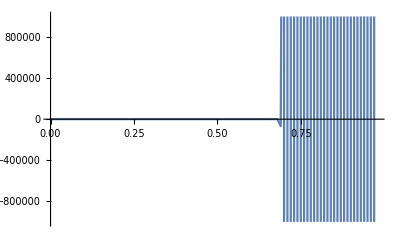

```mathematica
ListLinePlot[listTU,PlotRange->{Automatic,{-1000000,1000000}}]
```

```mathematica
Export["/home/ilya/brusselator/TUplotX=0.4du1dv100.png",ListLinePlot[listTU,PlotRange->{Automatic,{-1000000,1000000}}]]
```

/home/ilya/brusselator/TUplotX=0.4du1dv100.png

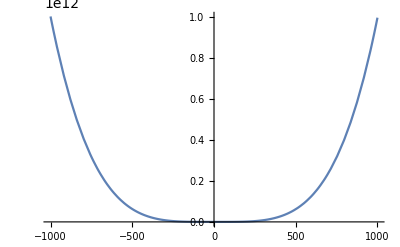

```mathematica
Plot[x^4- 3x^3+x^2-1,{x,-1000,1000}]
```

```mathematica
Solve[x^4-7 x^3+14 x^2- 7x+1==0,x]
```

{{x→2-√3},{x→2+√3},{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

```mathematica
Factor[x^4-7 x^3+14 x^2- 7x+1]
```

(1-4 x+x^2) (1-3 x+x^2)

```mathematica
y[x_]:=Im@Sqrt[x];
```

```mathematica
y[-1]
```

1

```mathematica
ClearAll@Dv
```

```mathematica
OwnValues@A
```

{}

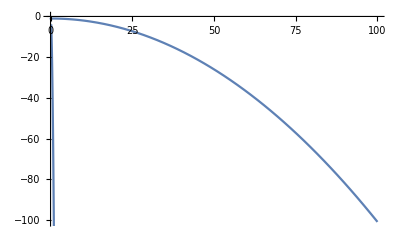

```mathematica
Assuming[{k∈Reals,k>0},
Block[{B=1,A=1,Du=0.01,Dv=100},
p1[k_] := 0.5*(B-1-A^2-(Du+Dv)k^2+Sqrt[(B-1-A^2-(Du-Dv)k^2)^2-4 A^2 B]);
p2[k_] := 0.5*(B-1-A^2-(Du+Dv)k^2-Sqrt[(B-1-A^2-(Du-Dv)k^2)^2-4 A^2 B]);
realp1[k_] :=Re@p1[k];
realp2[k_] :=Re@p2[k];
(*Print[{p1[x], " ", Re@p1[x], Im@p1[x], imp1[x]} /.x->0.16] *)
(*Export["/home/ilya/brusselator/p12(k)a1b1du100dv1.pdf",Show[Plot[realp1[k],{k,0,100}],Plot[realp2[k],{k,0,100}]]];*)
Show[Plot[realp1[k],{k,0,100}],Plot[realp2[k],{k,0,100}]]
]
]
```

```mathematica
Block[{B=2,A=1,Du=1,Dv=100},
FindInstance[(B-1-A^2-(Du-Dv)k^2)^2-4 A^2 B≥ 0,k]
]
```

{{k→2^(3/4)/(3 √11)}}

```mathematica
N@(2^(3/4)/(3 √11))
```

0.169027

```mathematica
With[{B=2,A=1,Du=1,Dv=100},
Reduce[((B-1-A^2-(Du-Dv)k)^2-4 A^2  B== 0)&&(k>0),k,Reals];
Plot[(B-1-A^2-(Du-Dv)k)^2-4 A^2  B,{k,-0.5,0.5}];
(B-1-A^2-(Du-Dv)k)^2-4 A^2  B/.k->0.02857
]
```

0.0000162649

```mathematica
N@(2^(3/4)/(3 √11))^2
```

0.02857

```mathematica
k≥Root[-8+9801 #1^4&,2]
```

k≥Root[-8+9801 #1^4&,2]

```mathematica
Simplify@Root[-8+9801 #1^4&,2]
```

Root[-8+9801 #1^4&,2]

```mathematica
(-8+9801 #^4)&[1]
```

9793

```mathematica
#1 &[1]
```

1

```mathematica
B=2;A=1;Du=1;Dv=100;
```

```mathematica
Reduce[(B-1-A^2-(Du-Dv)k^2)^2-4 A^2  B≥ 0&&k>0,k,Reals]
```

k≥Root[-8+9801 #1^4&,2]

```mathematica
(-8+9801 #^4)&[1]
```